```mathematica
P1=Import["P1.txt","Table"];
P2=Import["P2.txt","Table"];
```

```mathematica
μ=50;
nn=9;
wc=μ/(nn+3/2);
(*Ez=(3/4)*wc;*)
{Ez,me,α}={0.1*wc,1,0.0};
data={};V0=3;
For[V0=0.1,V0≤4,V0+=0.1,
{
l=1/Sqrt[me*wc];
kf[n_,s_]:=Re[Sqrt[2*me*(μ-((n+1/2)*wc-Sign[s]*Ez/2))]];
sn[n_,m_]:=(-1/Pi)*(1/l)*(kf[m,-1]*P1[[n+1,m+1]]-kf[m,+1]*P1[[n+2,m+1]]);
s[n_]:=Sum[sn[n,m],{m,0,nn+1}];
sm[n_,m_]:=Piecewise[{{s[n],n==m}},0];
smatrix=Table[sm[n,m],{n,0,nn},{m,0,nn}];
km[n_,m_]:=Piecewise[{{(1/Pi)*(kf[n,-1]-kf[n+1,+1]),n==m}},0];kmatrix=Table[km[n,m],{n,0,nn},{m,0,nn}];
vmatrix=Table[(1/l)*P2[[n+1,m+1]],{n,0,nn},{m,0,nn}];
M=-kmatrix.vmatrix-smatrix;
For[i=0,i≤nn,i++,
{mm=Eigenvalues[M][[i+1]];
ω=V0*mm+δϵ[0];
AppendTo[data,{V0*me,ω/wc}]}];
}]
```

```mathematica
Eigenvalues[M]
```

{0.63982004213477813308710711,0.61598654731822239641752233,0.57158806796440969199632342,0.46824934438900001750442859,-4.3918666619066129057632829×10^-30}

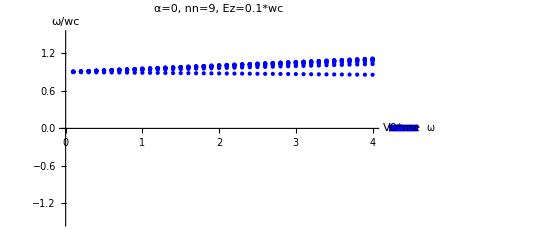

```mathematica
f1=ListPlot[data,PlotStyle->Blue,PlotRange->{{0,4},{-1.5,1.5}},PlotLegends->SwatchLegend[{Blue},{"ω"}],AxesLabel->{"V0*me","ω/wc"},PlotLabel->"α=0, nn=9, Ez=0.1*wc"]
```

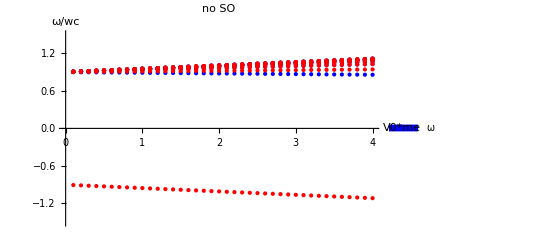

```mathematica
Show[f1,f2]
```

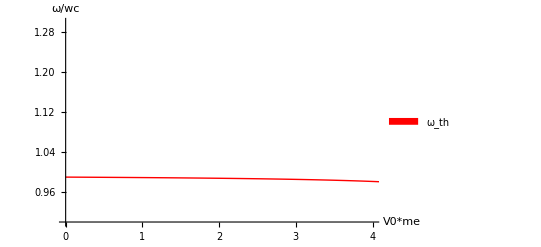

```mathematica
Clear[V0];f2=Plot[-(1/wc)*((Ez/wc)*wc*(1+(1/me)*(q)/(4*Pi-2*q))-Sqrt[((1/me)*q*(Ez/wc)*wc*me/(4*Pi-2*q))^2+wc^2]),{q,0,30},PlotStyle->Red,PlotRange->{{0,4},{0.9,1.3}},PlotLegends->SwatchLegend[{Red},{"ω_th"}],AxesLabel->{"V0*me","ω/wc"}]
```

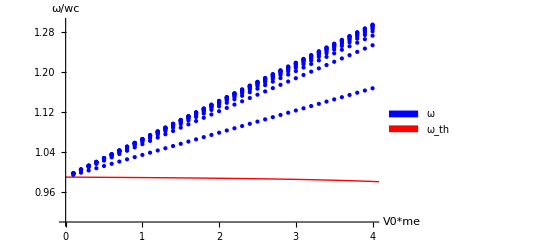

```mathematica
Show[f1,f2]
```